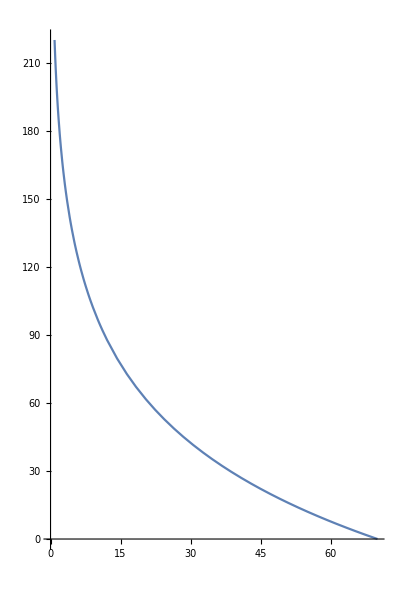

```mathematica
outputxy = Plot[-50*Log[x/70], {x, 0, 100}, PlotRange->{{0,70},{0,220}}, AspectRatio->1.5, LabelStyle->Opacity[0]]
```

```mathematica
-Graphics-
texturexy = Graphics3D[{Texture[outputxy],Polygon[{{0,0, 0},{220,00,0},{220, 220,0},{0,220,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics-

-Graphics3D-

```mathematica
processes = ParametricPlot3D[{{t,0,-50*Log[t/70]}, {t,100,-50*Log[t/70]}, {t,200,-50*Log[t/70]}, {t,-50*Log[t/70],0}, {70, t, 0}},{t,0,100}]
```

-Graphics3D-

```mathematica
Show[processes,ImageSize->Large]
```

-Graphics3D-

```mathematica
Show[texturexy,processes, ImageSize->Full, PlotRange->All,ImageSize->Full,BoxRatios->{1,1,1/2},Axes->True,AxesLabel->{x,y,z}, PlotStyle->Opacity[.2]]
```

-Graphics3D-

-Graphics3D-

```mathematica
#TestingOutaProcessPlane

graphic1=Plot3D[Exp[x],{x,0,2},{y,0,8},PlotStyle->Opacity[.2],MeshStyle->Opacity[0]]
```

#TestingOutaProcessPlane

-Graphics3D-

```mathematica
graphic2=Plot3D[Exp[x],{x,0,2},{z,0,8},PlotStyle->Opacity[.2],MeshStyle->Opacity[0]]
```

-Graphics3D-

-Graphics3D-

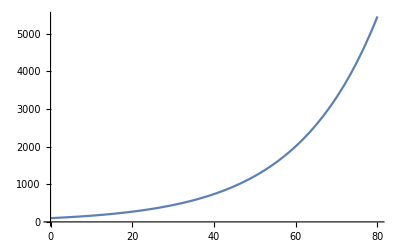

Show::gtype: Out is not a type of graphics.

Show[%230,ImageSize→Large]

```mathematica
Plot[100Exp[0.05*x], {x, 0, 80}]
```

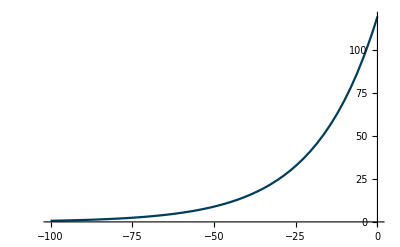

```mathematica
r3[x_] := Exp[0.052(x+92)] 
r4[x_] := 96  - 20Log[x]

interest3 = Plot[r3[x], {x, -100, 0}, 
PlotStyle->RGBColor[0, 0.24, 0.36]]
```

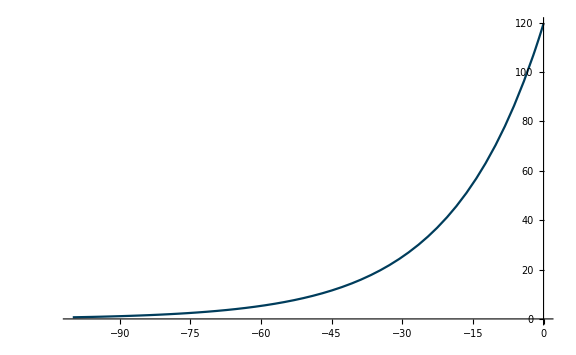

```mathematica
Show[interest3,ImageSize->Large]
```

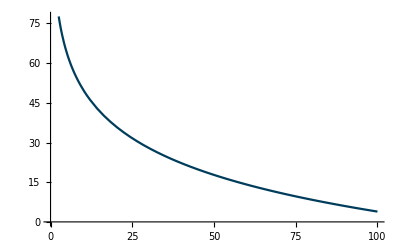

```mathematica
interest4 = Plot[r4[x], {x, 0, 100}, 
PlotStyle->RGBColor[0, 0.24, 0.36]]
```

-Graphics-

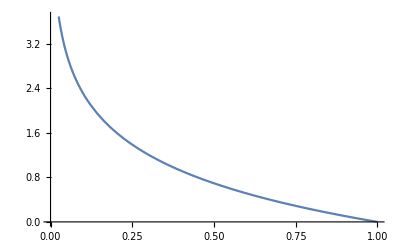

```mathematica
-Graphics-
Plot[-Log[x], {x, 0, 1}]
```

```mathematica
processgraphic1=ParametricPlot3D[{{t,1,z*-Log[t]}, {t,10,z*-Log[t]}, {t,5,z*-Log[t]}},{t,0,1},{z,0,1},BoundaryStyle->Directive[Thin,Black],BoxRatios->{1,1,1/2},PlotStyle->Opacity[.5],PlotRange->All]
```

-Graphics3D-

```mathematica
Show[processgraphic1,ImageSize->Large]
```

-Graphics3D-

```mathematica
testslice2=ContourPlot3D[z==-20Log[x/5],{x,0,7},{y,0,400},{z,0,100},ContourStyle->Opacity[0.1,Lighter@Green], Mesh->{{-5},{{2.25,Directive[Thin,Red]}, {50,Directive[Thin,Red]}}}, AxesLabel->{x, y, z}]
```

-Graphics3D-

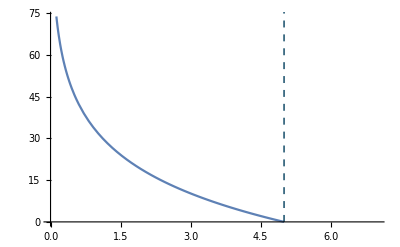

```mathematica
outputxy2 = Plot[-20Log[x/5], {x, 0, 5},TicksStyle->Directive[FontOpacity->0,FontSize->0],  
PlotRange->{{0,7},Automatic},
Epilog->{RGBColor[0, 0.24, 0.36],Dashed, Line[{{5,0},{5,400}}]}]
```

```mathematica
texturexy2 = Graphics3D[{Texture[outputxy2],Polygon[{{0,-10, 0},{7,-10,0},{7, 400,0},{0,400,0}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Show[texturexy2]
```

-Graphics3D-

```mathematica
Show[testslice2, texturexy2]
```

-Graphics3D-